```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0_2.0.txt","Table"];
list2 = Import[NotebookDirectory[]<>"/res/out_1.5_2.0.txt","Table"];
Length[list1]
len=Length[list2[[1]]]
```

50

501

```mathematica
maxlist1=Map[Max,-list1]/Max[-list1[[1]]];
maxlist2=Map[Max,-list2]/Max[-list2[[1]]];
```

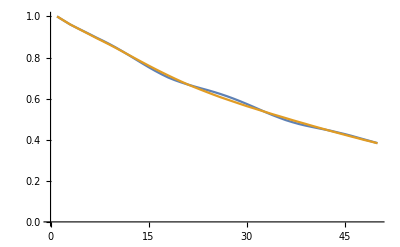

```mathematica
ListLinePlot[{maxlist1,maxlist2}]
```

```mathematica
enlist1=Map[Total[#^2]&,-list1];
enlist1=enlist1/Max[enlist1];
enlist2=Map[Total[#^2]&,-list2];
enlist2=enlist2/Max[enlist2];
```

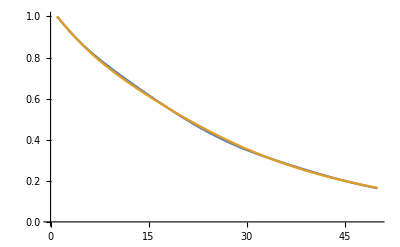

```mathematica
ListLinePlot[{enlist1,enlist2}]
```

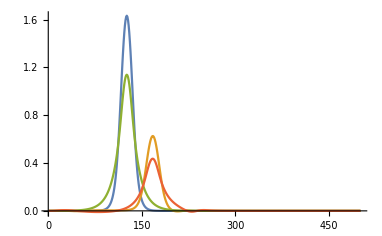

```mathematica
ListLinePlot[{-list1[[1]],-list1[[-1]],-list2[[1]],-list2[[-1]]},PlotRange->Full]
```

```mathematica
f1=NIntegrate[Interpolation[list[[1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[list[[-1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

44.376

7.27494

-0.836061

```mathematica
list1[[1]]
```

{<<<<<<<,HEAD}